## BIK-TZP vítejte na prvním interaktivním cvičení předmětu Technologické základy počítačů-Graphics-

Dříve BIK-CAO - jedná se v podstatě o identické předměty s rozdílnými názvy z důvodu nové akreditace,
ohledně Úvodu do Mathematicky není žádný rozdíl.

Vytvořeno na základě materiálů Miroslava Skrbka a Pavla Kubalíka.
Posledni úpravy: Martin Daňhel 2022

◀     |     ▶

## Co se naučíte v tomto předmětu ?

Naučíte se základům analogových a číslicových obvodů, analýza obovodů a simulaci.

Naučíte se pracovat v mocném programu Wolfram Mathematica, který budeme používat pro výpočty a simulaci obvodů

```mathematica
Solve[x^2+2x-4==0, x]//N
```

{{x→-3.23607},{x→1.23607}}

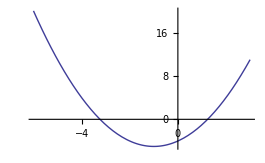

```mathematica
Plot[x^2+2x-4,{x,-6,3}]
```

◀     |     ▶

## Požadavky pro udělení zápočtu/známky

Nutné podmínky pro získání zápočtu

získání alespoň 20 bodů ze zápočtového testu

Možné body, které lze v semestru získat

Zápočtový test (max 40 bodů)

Aktivita (max 10 bodů)

Domácí úkoly - celkem 4 sady (max 20 bodů)

Získání známky A resp. B

Pokud student získá zápočet (napíše test na víc jak 20 bodů) a dále pak získá z aktivity a domácích úkoů v součtu 40-44 bodů, má nárok na známku B ze semestru, resp. 45-70 bodů má nárok na známku A ze semestru.

◀     |     ▶

## Domácí úkoly a hodnocení

Hodnocení

lze se dozvědět zde: http://grades.fit.cvut.cz

Domácí úkoly

Po každém cvičení se zpřístupní 1 sada domácích úkolů

Celkem jsou naplánovány 4 sady domácích úkolů

zadání/odevzdání probíhá přes tuto aplikaci: https://ddd.fit.cvut.cz/odevzdavac/ (je potřeba kliknout na odkaz Daňhel v části BIK-TZP (Sobota))

◀     |     ▶

## Wolfram Mathematica

Progam Wolfram Mathematica je mocný nástroj pro symbolické počítání. Je ho možno použít jako

kalkulačku

maticový kalkulátor

pro řešení lineárních rovnic s více proměnnými

řešení diferenciálních rovnic

symbolické derivování a integrování

vykreslování grafů

a spoustu dalších funkcí

◀     |     ▶

## Kde mohu pracovat s programem Mathematica ?

Ve cvičeních, kde je nainstalován na počítačích PC.

Program Mathematica si můžete (a my to velmi doporučujeme) nainstalovat na domácí počítač.

Instalační soubor si stáhnete na http://download.cvut.cz po přihlášení hlavním přístupovým heslem.

Pro program potřebujete licenci. Pro získání licence se řiďte pokyny na stránce předmětu BI-TZP.

Pokud budete mít s instalací problémy, sdělte to vašemu cvičícímu a pokuste se problém vyřešit. Ideální je přinést přímo notebook s instalovaným programem (pokud máte).

◀     |     ▶

## PC v učebně NTK:PU1 nebo T9:349

Přihlášení os Linux 

Pro přihlášení použijte přidělené celoškolské uživatelské jméno a heslo. Pokud jste se již v jiných cvičeních přihlašovali a změnili si heslo, tak musíte použít změněné heslo.
Program Mathematica spusťte tak, že vyhledáte v systémovém menu položku Console a v příkazovém řádku napíšete mathematica.

Soubory ukládáme na /home/stud/<vaše username>
Doporučujeme si vytvořit podadresář “tzp”, aby se vám soubory nepletly se soubory z jiných předmětů. Návod: v terminálu (Console) napíšeme: cd ; mkdir tzp

Přihlášení os Windows

Pro přihlášení použijte přidělené celoškolské uživatelské jméno a heslo. Pokud jste se již v jiných cvičeních přihlašovali a změnili si heslo, tak musíte použít změněné heslo.
Program Mathematica najdete v nabídce Start.

Soubory ukládáme na disk X:/
Doporučujeme si vytvořit podadresář "tzp", aby se vám soubory nepletly se soubory z jiných předmětů.

◀     |     ▶

## Mathematica - vytvoření notebooku, práce s buňkami

Notebook připomíná textový editor, který nám slouží jako rozhraní k výpočetnímu jádru programu Mathematica. Do notebooku píšeme matematické výrazy, komentáře v podobě formátovaného textu, zobrazují se nám zde výsledky výpočtů a grafy.

Notebook vytvoříme výběrem položky menu: Menu→File→New→Notebook

Notebook se skládá z buněk (Cell), které připomínají řádky (bloky) textu s proměnlivou výškou. Buňka může obsahovat více standardních řádků. Mezi buňkami přecházíme kurzorovými šipkami nahoru/dolů. Pozor! použití klávesy Enter znamená přidání řádku v rámci buňky, nikoliv přechod na další buňku.

Buňka je označena na pravé straně notebooku modrou skobičkou, na kterou můžeme kliknout myší a svinout buňku, rozvinout buňku, označit ji a pak klávesou delete vymazat.

Každá buňka má styl. Například: input - vstup pro výpočty, out - výstup výpočtu, text - text (dokumentace výpočtu), title - nadpis, ...      

Buňky lze spojovat a rozdělovat.

Při práci s notebookem je vhodné si otevřít panel matematických vstupů. Palettes → Other → Basic Math Input

Vzhledem k tomu, že je program Mathematica napsán jako Client ⟷ Server, jsou veškeré výpočty prováděny až po odeslání buňky na server s pomocí SHIFT+ENTER.

◀     |     ▶

## Čísla v programu Mathematica

Celá čísla (přesná)

```mathematica
{1,2,3,4,-5,1000};
```

Racionální čísla (přesná)

```mathematica
{4/3,-1/3,100/330};
```

Iracionální čísla (přesná)

```mathematica
{√6,ⅇ^5,π};
```

Komplexní (přesná, nepřesná pokud obsahují reálná čísla)

```mathematica
{1+3ⅈ,6-2ⅈ,8-6/5 ⅈ};
```

Reálná čísla (nepřesná)

```mathematica
{3.14,1.41,2.6545,-32.567};
```

◀     |     ▶

## Jednoduché výpočty

S programem Mathematica lze provádět i jednoduché výpočty.

3+4

5*8

2*π

Program Mathematica provádí všechny vypočty s ohledem na zachování přesnosti. Pokud chceme přesné čislo převést do nepřesné podoby (jako reálné číslo), použijeme funkci N[2π]. Pokud chceme počítat "nepřesně" (např. pro zrychlení výpočtu) můžeme čísla zadávat jako reálná. Např.: místo 2*π zadáme 2.*π

Různé způsoby volání funkce

Infixová forma		3 * 5

Postfixová forma	2π//N

Prefixová forma	N@ 2π

Vstupy lze zadávat s pomocí panelu Basic Math Input, popřípadě je možné využít klávesovou zkratku

Děleno		2/3	lze zadat jako 2 Ctrl+/ a 3

Mocnina	2^3	lze zadat jako 2 Ctrl+6 a 3

PI		π	lze zadat jako Esc p Esc

Odmocnina √3	lze zadat jako Ctrl+2 a 3

◀     |     ▶

## Proměnné

Proměnné jsou například x, y, k, L, ale také xx, x1, kocka, pes23, ...
Proměnná začíná písmenem (snažte se používat malá písmena), za kterým následuje žádný, jeden nebo více znaků nebo číslic.
Proměnná nesmí začínat číslem, např. 2x má význam 2 krát x tak, jak je užíváno v matematice (oboru).

Nepoužívat podtržítka, jako je to zvykem v jazyce C, např. x_1, podtržítko má v programu Mathematica zvláštní význam.
Pro jistotu nepoužívat ani indexy, mohou vést k nepředpokládanému chování programu.

```mathematica
{x,xx,kocka,pes,Subscript[x, 1],Subscript[xy, 3],a1,b787,abc4};
```

Pozor ! xy neznamená x krát y, ale jméno proměnné xy. Násobení zapisujeme x * y. Jako násobení se také chápe x y (mezera mezi x a y), to ale nepoužívejte, je to zdroj nepříjemných chyb.

Jména proměnných volte rozumně, spíše více písmen dávajících smysl (rovnice1, vstup, ...), zvyšuje to čitelnost programu.

◀     |     ▶

## Operátor =

Pro pochopení operátoru si představte, že program Mathematica obsahuje tabulku jmen proměnných a jejich hodnot (tabulku symbolů). Každá položka (řádek) obsahuje jméno proměnné a její hodnotu.

```mathematica
x=1;(* do proměnné x přiřaď jedničku *)
```

Např. po provedení x=1 obsahuje tabulka řádek pro x (na začátku předpokládáme prázdnou tabulku symbolů).

proměnná | hodnota
x | 1

```mathematica
y=2;(* do proměnné y přiřaď dvojku *)
```

proměnná | hodnota
x | 1
y | 2

Nyní jsou v tabulce symbolů dvě proměnné x a y s přiřazenými hodnotami.

◀     |     ▶

## Změna obsahu proměnné

```mathematica
x=1;
```

```mathematica
y=2;
```

Tabulka symbolů po provedení výše uvedených přiřazení

proměnná | hodnota
x | 1
y | 2

```mathematica
x=5;
```

Nyní jsme změnili obsah proměnné x.

proměnná | hodnota
x | 5
y | 2

◀     |     ▶

## Vyhodnocení jednoduchých výrazů

```mathematica
x=1;
y=2;
```

Tabulka symbolů  po provedení výše uvedených přiřazení

proměnná | hodnota
x | 1
y | 2

```mathematica
z=x+y;
```

Výraz x+y na pravé straně operátoru přiřazení se vyhodnotí tak, že se Mathematica pro x podívá do tabulky symbolů a nahradí ho jeho hodnotou (1 v našem případě), totéž udělá pro y a pak teprve provede součet. Pak bude tabulka symbolů vypadat takto:

proměnná | hodnota
x | 1
y | 2
z | 3

◀     |     ▶

## Funkční program

```mathematica
x=1;
y=2;
z=x+y;
```

```mathematica
z (* vytiskni obsah z *)
```

3

Zadání k vlastnímu řešení:

Vypočtěte hodnotu výrazu x^2+5y-6z pro hodnoty x=10, y=25, z=8
Výsledek bude uložen v proměnné r.

◀     |     ▶

## Záludnosti při vyhodnocení buněk v notebooku

Buňky v notebooku se vyhodnocují na vyžádání, a to buď

jednotlivě (v každé buňce stiskneme klávesy Shift-Enter)

pořadí vyhodnocení je dáno pořadím výběru buněk k vyhodnocení. Pokud vyhodnocujeme buňky na přeskáčku, může se stát, že dostaneme nesmyslné výsledky, protože si jádro vytváří tabulku symbolů v pořadí tak, jak vyhodnocujeme buňky a ne tak, jak jsou zapsány v notebooku. Navíc je možné některé pravidlo vyhodnotit vícekrát. Pokud děláme navíc v notebooku zásadnější změny, tak i přes to, že veškeré změny odesíláme do jádra (Shift-Enter), tak stav tabulky symbolů před změnami nám může způsobit nesmyslný výsledek.
	Proveďte:
		Menu→Evaluation→QuitKernel→Local        (zajistí vynulování tabulky symbolů, začínáme tedy s "čistým stolem")
		Shift+Enter na buňce z=x+y
			výsledek je x+y, protože ani x ani y nebylo zatím definováno (x=1 a y=2 nebylo ještě posláno do jádra).
		Shift+Enter na buňce y=2; a potom na z = x+y
			výsledek je x+2, protože y má hodnotu 2
		Shift+Enter na 	buňce x=1; a potom na z = x+y
			výsledek je 3, který jsme očekávali

hromadně (Menu→Evaluation→EvaluateNotebook)

Vyhodnotí všechny buňky v notebooku směrem od začátku do konce. Toto je významné, ale stále jen částečné řešení předchozího problému. Stále ještě hrozí, že před vyvoláním Menu→Evaluation→EvaluateNotebook nebyla tabulka symbolů prázdná a zvláště pokud používáme jednu proměnnou (jedno jméno) vícenásobně pro různé a nesouvisející výrazy, můžeme se stejně dobrat chybných výsledků. Pokud chceme mít jistotu, pak musíme inicializovat kernel (Menu→Evaluation→QuitKernel→Local) a vyhodnotit všechny buňky v notebooku  Menu→Evaluation→EvaluateNotebook.

Pozor! Pokud máme otevřeno více notebooků, pak všechny využívají jeden kernel. Tzn. proměnná nadefinovaná v jednom notebooku je viditelná v jiném notebooku.
Není to však pravidlem - v některých operačních systémech se při otevření uloženého notebooku spustí i nový samostatný kernel.

◀     |     ▶

## Řešení problémů s vyhodnocováním buněk

Před každou skupinou buněk, která řeší nějaký matematický problém, vymažeme funkcí ClearAll["Global`*"]; hodnoty všech proměnných v tabulce symbolů.

```mathematica
ClearAll["Global`*"];
x=1;
y=2;
z=x+y
```

3

Pak pokud použijeme funkci Menu→Evaluation→EvaluateNotebook, máme jistotu, že se nám všechny buňky vyhodnotí ve správném pořadí a navíc budou správně inicializovány. 
Toto si zvykneme psát do našich notebooků, abychom stále nenaráželi na problémy s vyhodnocováním buněk.
V případě, že je v notebooku více různých menších příkladů (typicky testy), umístíme každý z nich do jedné samostatné buňky a na její začátek vložíme funkci ClearAll[“Global`*”];

ClearAll můžeme použít i v případě, že potřebujeme smazat hodnoty pouze u vybraných promměnných:

```mathematica
ClearAll["Global`*"];
x=1;
y=1;
z=x+y;
ClearAll[x,y];
x
y
z (*z jsme nevymazali, tudiz si svou hodnotu pamatuje*)
```

x

y

2

◀     |     ▶

## Funkce (vestavěné)

Funkce v programu Mathematica hrají stejnou roli jako funkce v matematice.

Jsou zde pouze odlišnosti v zápisu. Např. sin(x) se zapíše jako Sin[x].

Vestavěné funkce začínají vždy velkým písmenem a argumenty (parametry) jsou uzavřeny v hranatých závorkách.

Funkce má určitý počet pevně určených parametrů a ostatní jsou volitelné a nezávisí na jejich pořadí. Volitelné parametry se zapisují jako pravidla, např. PlotRange→All.

Např. funkce Sin[x] má jeden pevný parametr. Funkce Plot[funkce, rozsah, PlotRange->All, ...] má dva pevné parametry funkce a rozsah, další parametry jsou volitené.

Význam jednotlivých parametrů funkcí nalezneme v helpu.

```mathematica
?Sin
```

RowBox[{"Sin", "[", StyleBox["z", "TI"], "]"}] gives the sine of StyleBox["z", "TI"].

```mathematica
?Plot
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

Pokud neznáme plně jméno funkce, stačí naznačit (napsat jen část) např. Arc a pak Ctrl-k. Mathematica napoví (objeví se pop-up menu s možnostmi).
V aktuálních verzích Mathamaticy se toto menu ukazuje během psaní názvu funkce už automaticky.

◀     |     ▶

## Funkce definované uživatelem

Uživatel programu Mathematica si může definovat vlastní funkci.

Parametry na levé straně přiřazení musí končit podtržítkem x_, yy_, případně x:_ nebo yy:_. Jedná se tzv. formální parametry, za které se v místě užití dosadí parametry skutečné. Formální parametry na pravé straně přiřazení podtržítko nemají.

Užívá se zde jiného operátoru přiřazení (:=). Ten je interpretován odlišně oproti operátoru =. U operátoru = je k levé straně (jméno proměnné, funkce, ...) v tabulce symbolů přiřazena hodnota (vyhodnocený výraz na pravé straně) okamžitě. U operátoru := dojde k nahrazení levé strany pravou až v době užití, kdy je znám ke každému formálnímu parametru odpovídající parametr skutečný. 
Např. sigmoida[a+3,1] se nahradí 1/(1+ⅇ^(-1*(a+3))) , kde výraz a+3 a konstanta 1 jsou skutečnými parametry.

Definujme logistickou funkci zvanou Sigmoida.

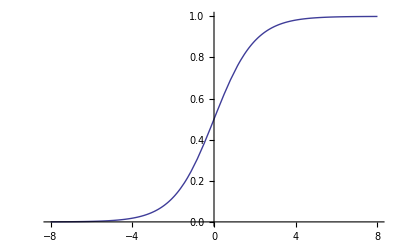

```mathematica
sigmoida[x_,γ_]:=1/(1+ⅇ^(-x*γ));

Plot[sigmoida[a,1],{a,-8,8}]
```

◀     |     ▶

## Kreslení grafů

Pro kreslení grafů (2D) používáme funkci Plot. První parametr je funkce, kterou chceme vykreslit. Druhý parametr je obor hodnot funkce pro zvolenou nezávislou proměnnou. Druhý parametr je vždy seznam obsahující po řadě proměnnou, minimální hodnotu a maximální hodnotu.

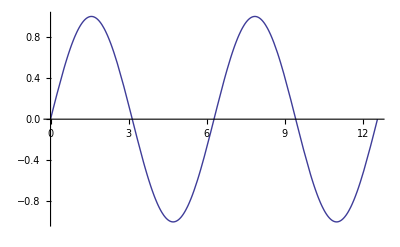

```mathematica
Plot[Sin[x],{x,0,4π}]
```

Pro kreslení grafů (3D) používáme funkci Plot3D. První parametr je funkce, kterou chceme vykreslit. Druhý a třetí parametr jsou obory hodnot funkcí pro zvolené nezávislé proměnné. Druhý i třetí parametr jsou vždy seznamy obsahující po řadě proměnnou, minimální hodnotu a maximální hodnotu.

```mathematica
Plot3D[Sin[x]+Sin[y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

Existují i další typy grafů (např. LogPlot, ParametricPlot, ListPlot, ListPlot3D, apod.) Detaily o těchto typech grafů lze nalézt v nápovědě.

◀     |     ▶

## Seznamy (List)

Seznam je datová struktura, která dovoluje sdružit více položek a definuje nad nimi množinu specifických operací.

Příklad seznamu:

```mathematica
ClearAll["Global`*"]
```

```mathematica
basaPiv={Gambrinus,Plzen,Staropramen}
basaPiv2={Bernard,Svijany,Rohozec}
hromadaPiv={basaPiv,basaPiv,basaPiv2,Starobrno,Radegast}
skladPiv={hromadaPiv,basaPiv2}
```

{Gambrinus,Plzen,Staropramen}

{Bernard,Svijany,Rohozec}

{{Gambrinus,Plzen,Staropramen},{Gambrinus,Plzen,Staropramen},{Bernard,Svijany,Rohozec},Starobrno,Radegast}

{{{Gambrinus,Plzen,Staropramen},{Gambrinus,Plzen,Staropramen},{Bernard,Svijany,Rohozec},Starobrno,Radegast},{Bernard,Svijany,Rohozec}}

Vybrané operace se seznamem:

```mathematica
(* první pivo v base *)
First[basaPiv]
```

Gambrinus

```mathematica
(* přidej nové pivo do basy *)
novaBasaPiv=Append[basaPiv,jesteJednaPlzen]
```

{Gambrinus,Plzen,Staropramen,jesteJednaPlzen}

```mathematica
?List
```

RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}] is a list of elements.

◀     |     ▶

## Přístup k prvkům seznamu (indexace)

K jednotlivým položkám listu lze přistupovat pomocí [[]] (po programátorsku: indexy polí se píšou do dvojitých hranatých závorek)

```mathematica
basaPiv[[2]]
```

Plzen

```mathematica
hromadaPiv[[3]]
```

{Bernard,Svijany,Rohozec}

```mathematica
hromadaPiv[[3,2]]
```

Svijany

```mathematica
skladPiv[[1]]
```

{{Gambrinus,Plzen,Staropramen},{Gambrinus,Plzen,Staropramen},{Bernard,Svijany,Rohozec},Starobrno,Radegast}

```mathematica
skladPiv[[1,2,3]]
```

Staropramen

◀     |     ▶

## Vícerozměrné seznamy

Příkladem vícerozměrného seznamu může být matice (3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)
Seznam odpovídající matici je sestaven po řádcích

```mathematica
matice={{3,12,5},{7,9,1},{22,11,10}}
```

{{3,12,5},{7,9,1},{22,11,10}}

```mathematica
prvekTretiRadekDruhySloupec=matice[[3,2]]
```

11

```mathematica
druhyRadek=matice[[2]]
```

{7,9,1}

```mathematica
prvniSloupec=matice[[All,1]]
```

{3,7,22}

Matice (i vektory) lze také zapsat pomocí palety Basic Math Assistant - sekce Basic Commands - ikona matice (□ | □
□ | □)
Paleta také obsahuje tlačítka pro přidávaní řádků (Ctrl + ⌤) a sloupců (Ctrl + ,).

```mathematica
matice2=({{3, 12, 5}, {7, 9, 1}, {22, 11, 10}})
matice2[[3,2]]
```

{{3,12,5},{7,9,1},{22,11,10}}

11

◀     |     ▶

## Funkce operující nad listy

```mathematica
?Flatten
```

RowBox[{"Flatten", "[", StyleBox["list", "TI"], "]"}] flattens out nested lists. 
RowBox[{"Flatten", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] flattens to level StyleBox["n", "TI"]. 
RowBox[{"Flatten", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["h", "TI"]}], "]"}] flattens subexpressions with head StyleBox["h", "TI"]. 
RowBox[{"Flatten", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["21", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["22", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] flattens StyleBox["list", "TI"] by combining all levels SubscriptBox[StyleBox["s", "TI"], StyleBox["ij", "TI"]] to make each level StyleBox["i", "TI"] in the result.

```mathematica
velkaHromadaPiv=Flatten[skladPiv]
```

{Gambrinus,Plzen,Staropramen,Gambrinus,Plzen,Staropramen,Bernard,Svijany,Rohozec,Starobrno,Radegast,Bernard,Svijany,Rohozec}

```mathematica
?Sort
```

RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}] sorts the elements of StyleBox["list", "TI"] into canonical order. 
RowBox[{"Sort", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["p", "TI"]}], "]"}] sorts using the ordering function StyleBox["p", "TI"].

```mathematica
srovnanaHromadaPiv=Sort[velkaHromadaPiv]
```

{Bernard,Bernard,Gambrinus,Gambrinus,Plzen,Plzen,Radegast,Rohozec,Rohozec,Starobrno,Staropramen,Staropramen,Svijany,Svijany}

```mathematica
?Union
```

RowBox[{"Union", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives a sorted list of all the distinct elements that appear in any of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Union", "[", StyleBox["list", "TI"], "]"}] gives a sorted version of a list, in which all duplicated elements have been dropped.

```mathematica
prebranaHromadaPiv=Union[velkaHromadaPiv]
```

{Bernard,Gambrinus,Plzen,Radegast,Rohozec,Starobrno,Staropramen,Svijany}

Další funkce lze najít v nápovědě (List Manipulation).

◀     |     ▶

## Funkce generující listy

```mathematica
?Range
```

RowBox[{"Range", "[", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "]"}] generates the list RowBox[{"{", RowBox[{"1", ",", "2", ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]. 
RowBox[{"Range", "[", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "]"}] generates the list RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]. 
RowBox[{"Range", "[", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "]"}] uses step StyleBox["di", "TI"].

```mathematica
Range[3,30]
Range[3,30,6]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

{3,9,15,21,27}

```mathematica
?Table
```

RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] generates a list of StyleBox["n", "TI"] copies of StyleBox["expr", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a list of the values of StyleBox["expr", "TI"] when StyleBox["i", "TI"] runs from 1 to SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] starts with RowBox[{StyleBox["i", "TI"], "=", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]]}]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "}"}]}], "]"}] uses steps StyleBox["di", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] uses the successive values SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ….
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["j", "TI"], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list. The list associated with StyleBox["i", "TI"] is outermost.

```mathematica
Table[x^2,{x,0,10}]
```

{0,1,4,9,16,25,36,49,64,81,100}

Další funkce lze najít v nápovědě (Constructing Lists).

◀     |     ▶

## Řešení soustavy lineárních rovnic

S řešením soustavy lineárních rovnic o dvou neznámých jste se setkali na střední škole.

Řešte následující soustavu rovnic
3x+2y=0
6x-4y=1

Použijeme funkci Solve

```mathematica
ClearAll["Global`*"]
Solve[{3x+2y==0,6x-4y==1},{x,y}]
```

{{x→1/12,y→-1/8}}

Matematické rovná se (=) se v programu Mathematica zapisuje jako == (dvě rovná se za sebou). Výsledkem výrazu je True (pravda) nebo False (nepravda). Například 5==6 dává False, ale 5==(6-1) dává True. Operátor == má prakticky stejný význam jako v jazycích C nebo Java.

Druhým parametrem funkce Solve je seznam neznámých proměnných.

◀     |     ▶

## Řešení soustavy diferenciálních rovnic

Diferenciální rovnice a jejich soustavy lze řešit v Mathematice buď analyticky pomocí funkce DSolve (výsledkem je funkce) nebo numericky pomocí NDSolve (výsledkem je popis grafu funkce pomocí interpolační funkce).
Hlavním rozdílem oproti klasickým lineárním rovnicím je nahrazení neznámých (x, y) za funkce (x[t], y[t]) a jejich derivace.

Řešte následující soustavu rovnic
3x[t]+2y[t]=x'[t]
6x[t]-4y[t]=1

Použijeme funkci DSolve

```mathematica
ClearAll["Global`*"]
DSolve[{3x[t]+2y[t]==x'[t],6x[t]-4y[t]==1},{x[t],y[t]},t]
```

{{x[t]→1/25 (25/12+ⅇ^(6 t) C[1]),y[t]→-1/4+3/50 (25/12+ⅇ^(6 t) C[1])}}

V rovnicích je opět nutno použít == (dvě rovná se za sebou).

Druhým parametrem funkce DSolve je seznam neznámých funkcí, třetí parametr je tzv. nezávisle proměnná, tj. ta proměnná, která se vyskytuje uvnitř závorek všech neznámých funkcí.

Ve výsledku řešení diferenciálních rovnic se vyskytuje konstanta C[1], kterou lze odstranit zadáním tzv. počáteční podmínky do soustavy. Soustava diferenciálních rovnic sice vypočítá tvar výsledné funkce, ale její přesné umístění je určeno právě počáteční podmínkou.

```mathematica
ClearAll["Global`*"]
resDS=DSolve[{3x[t]+2y[t]==x'[t],6x[t]-4y[t]==1,x[0]==0},{x[t],y[t]},t]
```

{{x[t]→1/12 (1-ⅇ^(6 t)),y[t]→1/8 (-1-ⅇ^(6 t))}}

◀     |     ▶

## Numerické řešení soustavy diferenciálních rovnic

Parametry numerického řešení pomocí NDSolve jsou velmi podobné jako u analytického řešení pomocí DSolve, pouze u třetího parametru je třeba zadat rozsah odkud kam bude výpočet probíhat.
Výsledek je pak možno použít jen v tomto rozsahu!

```mathematica
resNDS=NDSolve[{3x[t]+2y[t]==x'[t],6x[t]-4y[t]==1,x[0]==0},{x[t],y[t]},{t,0,1}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

Ve výsledku numerického řešení jsou vidět náhledy tvarů grafů všech neznámých funkcí.

Porovnání analytického a numerického řešení:

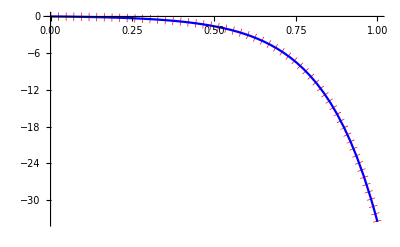

```mathematica
Plot[{x[t]/.resNDS[[1]],x[t]/.resDS[[1]]},{t,0,1},PlotStyle->{{Red,Dotted,Thickness[0.015]},{Blue}}]
```

Porovnání analytického a numerického řešení mimo rozsah NDSolve:

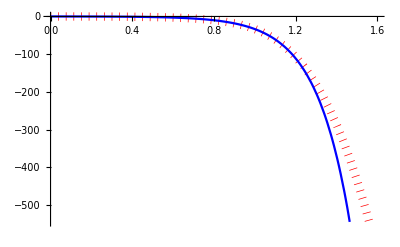

```mathematica
Plot[{x[t]/.resNDS[[1]],x[t]/.resDS[[1]]},{t,0,1.6},PlotStyle->{{Red,Dotted,Thickness[0.015]},{Blue}}]
```

◀     |     ▶

## Proměnné - rozšířené možnosti

Hodnotou proměnné může být nejenom číslo, ale prakticky jakýkoliv výraz či řetězec. Například:

```mathematica
x=5
budova=NTK
```

5

NTK

Proměnné lze proto využít například pro pojmenování složitých výrazů, například rovnic. Soustavu lineárních rovnic

2a + 3b + 4.2c == 5
3a + 15.2b + 8.7c == 80.1
4a + 8.9b + 17.2c == 11

lze proto řešit buď takto:

```mathematica
Solve[{2a+3b+4.2c==5,3a+15.2b+8.7c ==80.1,4a+8.9b+17.2c ==11}]
```

{{a→-3.63596,b→7.29908,c→-2.29174}}

nebo takto:

```mathematica
rce1=2a+3b+4.2c==5;
rce2=3a+15.2b+8.7c==80.1;
rce3=4a+8.9b+17.2c==11;
Solve[{rce1,rce2, rce3}]
```

{{a→-3.63596,b→7.29908,c→-2.29174}}

proměnná | hodnota
rce1 | 2a+3b+4.2c==5
rce2 | 3a+15.2b+8.7c==80.1
rce3 | 4a+8.9b+17.2c==11

◀     |     ▶

## Pravidla

```mathematica
ClearAll[x]
```

```mathematica
def={x->2,y->1,z->4}
moje={x-> 5}
{x,y,z}/.moje
({x,y,z}/.moje)/.def
```

{x→2,y→1,z→4}

{x→5}

{5,y,z}

{5,1,4}

"→"  se napíše tak, že zadáte - následované > a pak pokračujete v psaní. Stejný znak se používá i nepovinných parametrů (např.: Plot[Sin[x],{x,0,1},PlotStyle→Red])
Pozor při kopírování z pdf souborů, textových polí a ze stránek Courses! Často zkopírují netisknutelné a neviditelné znaky - problémy jsou zejména právě se znakem →, ale i s uvozovkami, indexy apod.

```mathematica
spatne=x->2;(*RightArrow*)
dobre=x->2;(*Rule*)
x/.spatne
x/.dobre
```

ReplaceAll::reps: {x→2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.x→2

2

```mathematica
FullForm[spatne]
FullForm[dobre]
```

RightArrow[x,2]

Rule[x,2]

◀     |     ▶

## Použití pravidel

S pravidly se setkáme nejčastěji jako s výsledkem funkce Solve (DSolve i NDSolve):

```mathematica
rce1=2a+3b+4.2c==5;
rce2=3a+15.2b+8.7c==80.1;
rce3=4a+8.9b+17.2c==11;
reseni=Solve[{rce1,rce2, rce3}]
a/.reseni
a+2*b/.reseni[[1]]
```

{{a→-3.63596,b→7.29908,c→-2.29174}}

{-3.63596}

10.9622

Je ale možné je použít i jako jednorázové dosazení v případě, že nechceme nedopatřením přepsat původní výraz

```mathematica
ClearAll["Global`*"]
```

Při prvním odpálení následující buňky je výsledek v pořádku, ale při druhém se vykreslí už jen rovná čára - do původního výrazu se při druhém odpálení uložila již dosazená konstanta x.

Cos[x]+Sin[x]

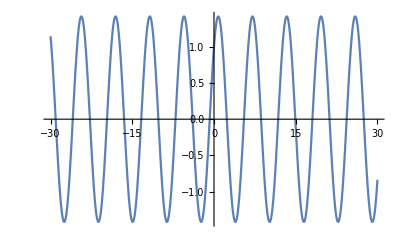

-1

```mathematica
mujVyraz=Sin[x]+Cos[x]
Plot[mujVyraz,{x,-30,30}]
x=π;
mujVyraz
```

```mathematica
ClearAll["Global`*"]
```

Následující buňku lze odpalovat opakovaně beze změny výsledku - aplikací pravidla se do x ani do výrazu nic neuložilo

```mathematica
mujVyraz=Sin[x]+Cos[x]
Plot[mujVyraz,{x,-30,30}]
mujVyraz/.x->π
```

Cos[x]+Sin[x]

-Graphics-

-1

◀     |     ▶

## Práce s maticemi (vícerozměrnými seznamy)

Zobrazení matice v matematickém tvaru pomocí MatrixForm:

```mathematica
ClearAll["Global`*"];
matice={{3,12,5},{7,9,1},{22,11,10}}
MatrixForm[matice]
```

{{3,12,5},{7,9,1},{22,11,10}}

(3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)

Pozor: Neukládejte MatrixForm[matice] do proměnné - Mathematica by pak už takovou matici neuměla dále zpracovat.
MatrixForm (a ostatní příkazy typu *Form - viz nápověda) slouží pouze pro zobrazení výsledku v čitelnější formě.

Tip: Pro příkazy typu *Form je výhodná postfixová notace zápisu.

```mathematica
matice//MatrixForm
```

(3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)

Maticové operátory a výpočty (viz nápověda Matrix Operations):

```mathematica
matice={{3,12,5},{7,9,1},{22,11,10}};
matice2=({{1, 2, 5}, {7, 8, 1}, {1, 4, 3}});
matice+matice2//MatrixForm (*součet*)
Transpose[matice]//MatrixForm (*tranzpozice*)
{a,b,c}.{x,y,z} (*skalární součin*)
{{a,b},{c,d}}*{x,y}//MatrixForm (*maticový součin*)
```

(4 | 14 | 10
14 | 17 | 2
23 | 15 | 13)

(3 | 7 | 22
12 | 9 | 11
5 | 1 | 10)

a x+b y+c z

(a x | b x
c y | d y)

◀     |     ▶

## Práce s maticemi (vícerozměrnými seznamy)

Zobrazení matice v matematickém tvaru pomocí MatrixForm:

```mathematica
ClearAll["Global`*"];
matice={{3,12,5},{7,9,1},{22,11,10}}
MatrixForm[matice]
```

{{3,12,5},{7,9,1},{22,11,10}}

(3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)

Pozor: Neukládejte MatrixForm[matice] do proměnné - Mathematica by pak už takovou matici neuměla dále zpracovat.
MatrixForm (a ostatní příkazy typu *Form - viz nápověda) slouží pouze pro zobrazení výsledku v čitelnější formě.

Tip: Pro příkazy typu *Form je výhodná postfixová notace zápisu.

```mathematica
matice//MatrixForm
```

(3 | 12 | 5
7 | 9 | 1
22 | 11 | 10)

Maticové operátory a výpočty (viz nápověda Matrix Operations):

```mathematica
matice={{3,12,5},{7,9,1},{22,11,10}};
matice2=({{1, 2, 5}, {7, 8, 1}, {1, 4, 3}});
matice+matice2//MatrixForm (*součet*)
Transpose[matice]//MatrixForm (*tranzpozice*)
{a,b,c}.{x,y,z} (*skalární součin*)
{{a,b},{c,d}}*{x,y}//MatrixForm (*maticový součin*)
```

(4 | 14 | 10
14 | 17 | 2
23 | 15 | 13)

(3 | 7 | 22
12 | 9 | 11
5 | 1 | 10)

a x+b y+c z

(a x | b x
c y | d y)

◀     |     ▶

## Derivace a integrály

Můžeme je napsat pomocí funkcí, nebo pomocí palety BasicMath Assistant v sekci Basic Commands:

```mathematica
D[x^n,x]
D[x^n, x]
```

n x^(-1+n)

n x^(-1+n)

Derivaci uživatelsky definované funkce můžeme napsat i pomocí apostrofu:

```mathematica
mojeFce[x_]:=x^n
mojeFce'[x]
```

n x^(-1+n)

```mathematica
Integrate[n x^(-1+n),x]
∫n x^(-1+n)ⅆx
```

x^n

x^n

Určitý integrál:

```mathematica
Integrate[ⅇ^-x,{x,1,Infinity}]
∫_1^∞ ⅇ^-x ⅆx
```

1/ⅇ

1/ⅇ

◀     |     ▶

## Boolova algebra

Výrazy můžeme psát v programátorském i matematickém tvaru:

```mathematica
a||b&&!c
boolVyraz=a∨b∧¬c
```

a||(b&&!c)

a||(b&&!c)

```mathematica
boolVyraz//TraditionalForm
```

a∨(b∧¬c)

Generování tabulky a mapy z funkce:

```mathematica
BooleanTable[boolVyraz,{a,b,c}] (*začíná od samých 1 (True)*)
```

{True,True,True,True,False,True,False,False}

```mathematica
BooleanTable[boolVyraz,{a},{b},{c}]//TableForm
```

True
True | True
True
False
True | False
False

Minimalizace výrazu a test tautologie:

```mathematica
BooleanMinimize[a∧b∨¬a∧b]
```

b

```mathematica
TautologyQ[(a||b)||(!a&&!b),{a,b}]
```

True

Další funkce lze najít v nápovědě (Boolean Computation).

◀     |     ▶

## Wolfram Alpha

K dispozici na adrese http://www.wolframalpha.com/ i bez nainstalované Mathematicy.
Výrazy můžeme zadávat v syntaxi Mathematicy i v běžné angličtině.
Z Mathematicy lze zadat dotaz pro Wolfram Alpha pomocí znaků ==, které zadáme na začátku nové buňky.

ursa major

iss today

Answer to the Ultimate Question of Life, the Universe, and Everything

Doctor John Zoidberg-like curve

◀     |     ▶

## Wolfram Alpha

K dispozici na adrese http://www.wolframalpha.com/ i bez nainstalované Mathematicy.
Výrazy můžeme zadávat v syntaxi Mathematicy i v běžné angličtině.
Z Mathematicy lze zadat dotaz pro Wolfram Alpha pomocí znaků ==, které zadáme na začátku nové buňky.

ursa major

iss today

Answer to the Ultimate Question of Life, the Universe, and Everything

Doctor John Zoidberg-like curve

◀     |     ▶